### Buch WiWi-Statistik Bamberg Kap 6, S59ff, Saisonbereinigung

Regression - Funktion für ein Jahr (mit 5 Monaten) :

```mathematica
regFuYear[x_]:= Piecewise[{{-x+5, x<1},{(x-2)^2+3, 1<=x<4},{x+3, x>=4}}]
```

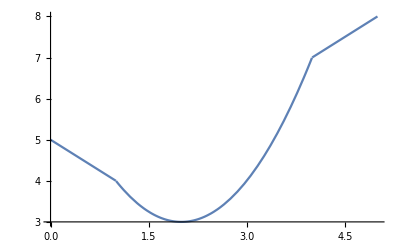

```mathematica
Plot[regFuYear[x], {x,0,5}]
```

Regression Funktion für 5 Jahre :

```mathematica
regFu5Year[x_]:=Module[{addY=3 , mons=5},  
Piecewise[Table[{regFuYear[x-i*mons]+i*addY, i*mons≤x<(i+1)*mons}, {i, 0, 4}]]]
```

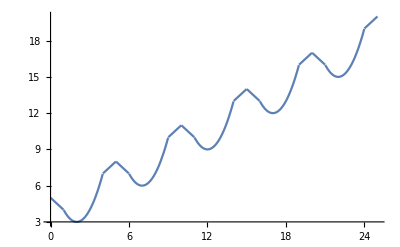

```mathematica
Plot[regFu5Year[x], {x,0,25}]
```

Time - Line für ein Jahr (Zufallszahlen eines Jahres) :

```mathematica
timeLiYear=Table[(regFuYear[i]+RandomReal[{-.2,.2}]), {i,0,5,.1}]
```

{4.86776,4.95868,4.91778,4.78974,4.70461,4.57,4.36636,4.4787,4.25729,4.02835,4.16204,3.61851,3.60674,3.4451,3.31619,3.26986,3.19598,3.03638,3.22513,2.96199,3.07616,3.02115,3.17109,3.20968,3.18134,3.11039,3.53541,3.47343,3.61095,3.69495,3.99041,4.2227,4.55695,4.61548,4.84331,5.09019,5.39571,5.70196,6.24832,6.54884,7.11006,7.21248,7.08714,7.25356,7.56461,7.37488,7.55097,7.53335,7.7613,8.01398,7.99673}

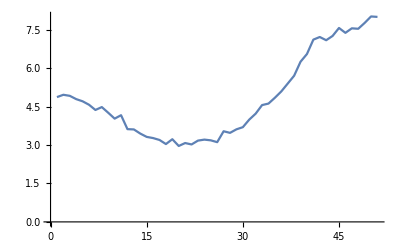

```mathematica
ListLinePlot[timeLiYear]
```

Zufallszahlen mit Trend für 5 Jahre :

```mathematica
getTimeLine5Year[gape_]:=Module[ {step=.1}, 
Table[regFu5Year[i]+RandomReal[{-gape,gape}], {i,0,24.99999,step}]]
```

```mathematica
timeLi5Year=getTimeLine5Year[.2];
```

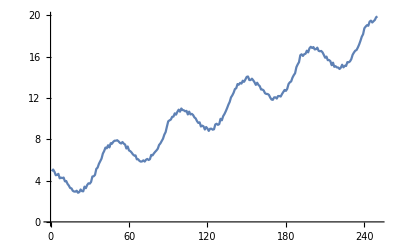

```mathematica
ListLinePlot[timeLi5Year]
```

```mathematica
DynamicModule[{d=.5, li}, {Slider[Dynamic@d,{.01,10, .01} ], Dynamic@d , Button["save list",  outLT5Y=li], Dynamic@ListLinePlot[li=getTimeLine5Year[d], ImageSize->Large]}]
```

```mathematica
outLT5Y
```

{5.07477,5.23681,4.44836,4.08643,5.24993,4.53694,4.92649,3.65664,5.08279,3.43858,3.83923,4.45537,3.55191,4.15621,3.59138,2.74436,3.58672,3.5631,3.70891,2.37503,2.7354,3.54008,2.32781,3.18803,3.61683,2.48812,4.0406,4.40696,3.62613,4.63004,4.27128,4.69589,3.61015,5.4021,4.3402,5.01927,5.2283,6.30033,5.96466,6.19802,6.71135,7.35369,7.15,7.73372,8.0851,7.42784,7.24057,6.80757,8.31345,8.55402,8.79011,8.60074,8.54326,7.72045,6.99017,7.52978,6.51607,7.03177,7.6321,7.2294,7.63737,7.47024,6.90929,6.09366,5.40315,5.26375,5.92702,5.31501,5.27599,6.59943,5.24946,5.42227,6.35355,5.31485,6.97328,6.67876,6.27191,6.22683,6.02259,6.654,7.86718,7.4531,7.13072,7.20812,8.0341,7.81873,8.64776,8.03324,9.91466,10.4762,9.5318,9.50142,10.1656,10.1422,10.8403,10.4125,11.6058,10.4302,11.3905,10.2542,10.3734,11.6666,10.2749,11.4994,9.78675,9.98145,9.90625,10.5446,10.1675,10.7633,10.9094,10.8183,10.2357,9.48788,9.8744,8.55378,9.20632,8.24807,8.74829,8.71013,8.04411,9.52521,8.84447,8.84304,8.80897,8.62536,8.83667,9.2762,9.54428,8.95398,10.065,11.1849,10.2156,10.171,11.4055,11.3554,10.7665,11.9086,12.5488,12.8137,12.1595,12.9694,13.5722,12.6086,13.9629,13.4516,14.598,14.6623,14.4747,13.8044,13.1176,12.9313,13.1083,13.1523,13.8835,14.0244,14.1242,13.7049,13.5379,12.8061,13.5407,12.0901,13.4198,13.4409,11.8196,12.1669,12.9241,11.1722,12.257,12.5314,11.3244,12.8913,12.3357,12.2079,12.0206,12.4681,12.7247,13.4833,12.0219,11.9809,12.4305,13.0418,14.1093,14.5263,13.1818,13.7335,13.5981,14.8152,16.0556,16.393,16.0822,15.2021,15.8109,15.4398,17.0532,16.4341,16.871,16.8939,17.4464,17.1369,17.6053,16.6784,16.0194,17.2526,16.7717,15.8114,16.3799,16.215,16.1129,16.8449,16.6266,16.0118,15.3858,15.7039,15.9974,15.5255,16.054,14.589,14.4087,15.8465,14.9863,14.1702,14.5884,15.2097,15.7219,14.5025,15.6887,15.6178,15.8536,16.4871,15.3945,16.8192,16.6658,16.8878,17.4665,16.9209,17.5759,18.6097,18.3101,19.0578,18.931,18.9688,19.503,20.1189,19.1984,18.9909,19.3368,19.4596,19.3438,19.0228}

Bemerkung: Bis Seite 61 ist das Model -> Trend (allg. i.a. Linear), Session (i.a. Jahreszeit), Konjunktur 
Dafür wird im Buch nicht gerechnet (nur Annahmen 1 ... 3, Seite 61)

Rechnung gleitender Mittelwert :

```mathematica
shiftMean[li_,wi_]:=Module[{lii, ku, hwi, lli, t1, t2, t3}, hwi=Floor[wi/2]; 
lii=li/wi//N; ku=Plus@@lii[[1;;wi]]; t1=Table[0,hwi]; 
lli=Length[li];  t2=Table[ku=ku-lii[[i-wi]]+lii[[i]], {i,wi+1, lli}];
t3=Table[0,lli-Length[t2]-hwi]; Flatten[{t1,t2,t3}]]
```

```mathematica
DynamicModule[{width=25}, {Slider[Dynamic@width, {2,100,1}], Dynamic@width, Dynamic@ListLinePlot[{outLT5Y,shiftMean[outLT5Y, width]}, ImageSize->Large] }]
```